# with crap signal

```mathematica
modfreqs={1,.5,.5,.5,.25,.1,.75,.9};
Tx=Flatten[{{{{1,0.11521977881233895},ErrorBar[0.02888661551338559]}},
{{{1,0.434776869966202},ErrorBar[0.12990358059797455]}},
{{{1,0.48225761844190196},ErrorBar[0.06527387056954334]}},
{{{1,0.6692169832603473},ErrorBar[0.09926311350909009]}},
{{{1,0.3031214292105065},ErrorBar[0.05602349451278461]}},
{{{1,0.16425879027986443},ErrorBar[0.044202819589689246]}},
{{{1,0.5621720934428515},ErrorBar[0.026589867945549968]}},
{{{1,0.20019237199954215},ErrorBar[0.01839087744739617]}}},1];
Ty=Flatten[{{{{1,0.4467151530156491},ErrorBar[0.034044637909758015]}},
{{{1,2.0996372327632113},ErrorBar[0.4135051995398317]}},
{{{1,2.8974907820899407},ErrorBar[0.2164657400860118]}},
{{{1,3.320241193683355},ErrorBar[0.3188479047031813]}},
{{{1,2.930968541469576},ErrorBar[0.49763771129191686]}},
{{{1,1.2962745856146574},ErrorBar[0.12554920520957336]}},
{{{1,0.48690970240927545},ErrorBar[0.027084064059731766]}},
{{{1,0.4888392599646279},ErrorBar[0.022297868044360188]}}},1];
```

```mathematica
Head[1.2]
```

Real

```mathematica
Cases[ToExpression[StringSplit[ToString[Tx[[;;,2]]],{"]","[","ErrorBar"}]],x_/;Head[x]==Real]
```

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before ", ".
                                                  ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation.

{0.0288866,0.129904,0.0652739,0.0992631,0.0560235,0.0442028,0.0265899,0.0183909}

# with only good signal

ErrorBar::shdw: Symbol "ErrorBar" appears in multiple contexts {"ErrorBarPlots`", "Global`"}; definitions in context "ErrorBarPlots`" may shadow or be shadowed by other definitions.

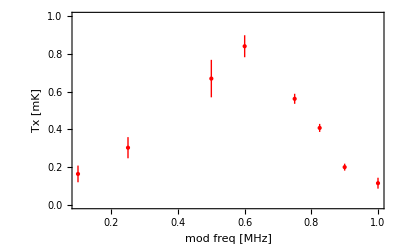

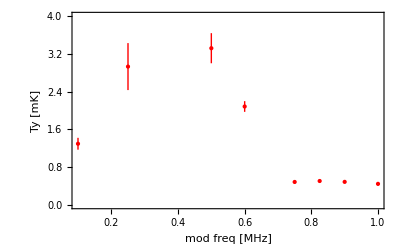

```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"];

mNa=3.81923952 10^-26;
mCs=2.207 10^-25;
kB = 1.3806488 10^-23;
m=mCs;

modfreqs={1,.5,.25,.1,.75,.9,.6,.825};
Tx=Flatten[{{{{1,0.11521977881233895},ErrorBar[0.02888661551338559]}},
{{{1,0.6692169832603473},ErrorBar[0.09926311350909009]}},
{{{1,0.3031214292105065},ErrorBar[0.05602349451278461]}},
{{{1,0.16425879027986443},ErrorBar[0.044202819589689246]}},
{{{1,0.5621720934428515},ErrorBar[0.026589867945549968]}},
{{{1,0.20019237199954215},ErrorBar[0.01839087744739617]}},
{{{1,0.8405112530946113},ErrorBar[0.05823550350576732]}},
{{{1,0.4078915915999675},ErrorBar[0.021313474403394612]}}},1];

Ty=Flatten[{{{{1,0.4467151530156491},ErrorBar[0.034044637909758015]}},
{{{1,3.320241193683355},ErrorBar[0.3188479047031813]}},
{{{1,2.930968541469576},ErrorBar[0.49763771129191686]}},
{{{1,1.2962745856146574},ErrorBar[0.12554920520957336]}},
{{{1,0.48690970240927545},ErrorBar[0.027084064059731766]}},
{{{1,0.4888392599646279},ErrorBar[0.022297868044360188]}},
{{{1,2.0854450283414647},ErrorBar[0.11326601324487226]}},
{{{1,0.5071783829396338},ErrorBar[0.028313469006225663]}}},1];

TX=Thread[{modfreqs,Tx[[;;,1,2]]}];
TxErr=Thread[{TX,Tx[[;;,2]]}];

TY=Thread[{modfreqs,Ty[[;;,1,2]]}];
TyErr=Thread[{TY,Ty[[;;,2]]}];

ErrorListPlot[TxErr,Axes->False,Frame->True, FrameLabel->{"mod freq [MHz]","Tx [mK]"},PlotStyle->{Thick,Red},PlotRange->{All,{0,1}}]
ErrorListPlot[TyErr,Axes->False,Frame->True, FrameLabel->{"mod freq [MHz]","Ty [mK]"},PlotStyle->{Thick,Red},PlotRange->{All,{0,4}}]
```

## velocity

```mathematica
(*get errors alone*)
Txerrs=Cases[ToExpression[StringSplit[ToString[Tx[[;;,2]]],{"]","[","ErrorBar"}]],x_/;Head[x]==Real];Tyerrs=Cases[ToExpression[StringSplit[ToString[Ty[[;;,2]]],{"]","[","ErrorBar"}]],x_/;Head[x]==Real];

(*speed at given temp*)
vx=√((kB TX[[;;,2]] /1000)/m);
vy=√((kB TY[[;;,2]] /1000)/m);
(*time to cross one micron*)
tx=10^-6/vx;
ty=10^-6/vy;

(*min switching freq reqd to confine atom based on simple model*)
fx=1/tx;
fy=1/ty;

(*propagate errors*)
fxerrs=(1/2)/(√TX[[;;,2]])√((kB  /1000)/m)10^6 Txerrs;
fyerrs=(1/2)/(√TY[[;;,2]])√((kB  /1000)/m)10^6 Tyerrs;
```

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before ", ".
                                                  ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

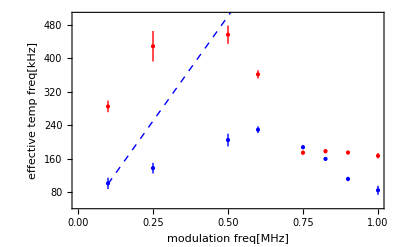

```mathematica
Show[{
ErrorListPlot[Thread[{Thread[{modfreqs,fy/1000}],
ErrorBar[#]&/@(fyerrs/1000)}],PlotRange->{50,500},FrameLabel->{"modulation freq[MHz]","effective temp freq[kHz]","blue,red = x,y-dir"}],

ErrorListPlot[Thread[{Thread[{modfreqs,fx/1000}],
ErrorBar[#]&/@(fxerrs/1000)}],PlotStyle->Blue],

Plot[1000x,{x,Min[modfreqs],Max[modfreqs]},PlotStyle->{Dashed,Blue}]
}]
```

## trap freq

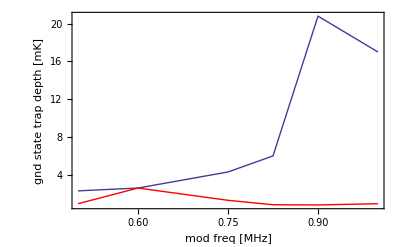

```mathematica
modfreqs={1,.5,.75,.9,.6,.825};
min={.94,.94,1.3,.81,2.6,.83};
max={17,2.3,4.3,20.8,2.6,6};
MIN=Sort[Thread[{modfreqs,min}]];
MAX=Sort@Thread[{modfreqs,max}];
ListPlot[{MAX,MIN},PlotStyle->{Thick,Red},Joined->True,PlotRange->All,FrameLabel->{"mod freq [MHz]","gnd state trap depth [mK]"}]
```

## trap freq as a fn of trap depth

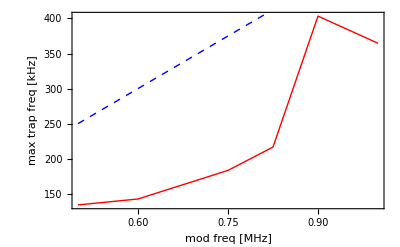

```mathematica
Cstrap1=88.42990274864627 √x;
Cstrap2=21.672940720882366 √x;
(*max allowed trap freq as a fn of modulation freq*)
maxfreq=Sort@Thread[{modfreqs,Cstrap1/.x->max}];
Show[{
ListPlot[maxfreq,Joined->True,FrameLabel->{"mod freq [MHz]","max trap freq [kHz]"}],
Plot[1000x/2,{x,maxfreq[[1,1]],maxfreq[[-1,1]]},PlotStyle->{Dashed,Blue}]
}]
```